```mathematica
(*Avtomatsko shranjevanje notebook-a*)
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Prva domača naloga 2025/26

## 1. Naloga

Seštej prvih 50 decimalk  števila . Rešitev zapiši v eni vrstici.

```mathematica
DigitSum[IntegerPart[(356/745)10^50],10,50]
```

257

```mathematica
(*Total[First[RealDigits[356/745,10,50]]] *)
```

## 2. Naloga

V spremenljivko `izraz` shrani izraz , v spremenljivko `izraz1` pa  .

```mathematica
izraz = Log[10, E]/Cos[Pi/4]^2 + (x+2)/10 + x;
```

```mathematica
izraz1 = Log[E]/Cos[Pi/4]^2 + (x+2)/10 + x;
```

a) Vse pojavitve parametra x v izrazu `izraz` zamenjaj z (x+1)^2. Dobljeni izraz shrani v `izraz2`.

```mathematica
izraz2 = izraz1 /.x->(x+1)^2
```

2+(1+x)^2+1/10 (2+(1+x)^2)

b) Izračunaj vrednost `izraz`-`izraz1` in dobljeno število čim bolj poenostavi. Nato izračunaj numerično vrednost dobljenega števila na 15 decimalnih mest natančno.

```mathematica
b = FullSimplify[izraz-izraz1]
```

-2+2/Log[10]

```mathematica
N[b,15]
```

-1.1314110361935

c) Definiraj funkcijo , ki kot argument sprejme realno število  in vrne numerično vrednost `(izraz+izraz1)/izraz2` pri x=n. Izračunaj f(2).

```mathematica
f[n_]:=N[(izraz+izraz1)/izraz2/.x->n]
```

```mathematica
f[2]
```

0.633768

d) Za funkcijo  iz dela c) poenostavi izraz  za x = 6, y = -1/2 in z = -1.

```mathematica
f[Log[3,x^2-8x z+3y-(x-3)^2]/.{x->6,y->-1,z->-1}]
```

0.414698

## 3. Naloga

a) Napiši  funkcijo `vrednostSin`, ki  bo  sprejela  število `x`, izračunala numerično vrednost števila `sin(x)` in  rezultat  izpisala  v  obliki
“Numerična vrednost sin([x]) je enaka [numericna_vrednost].”,
kjer [x] nadomestiš z vnešeno vrednostjo, [numericna_vrednost] pa z numerično vrednostjo sinusa pri vnešenem x na 7 decimalk natančno. Izračunaj `vrednostSin[-π/4]`.

```mathematica
vrednostSin[x_]:="Numerična vrednost sin("<>ToString[x]<>") je enaka "<>ToString[N[Sin[x],7]]<>"."
```

```mathematica
vrednostSin[-Pi/4]
```

Numerična vrednost sin(  1
-(-) Pi
  4) je enaka -0.7071068.

b) Definiraj anonimno funkcijo g (s parametrom #) s predpisom . Izračunaj g(6).

```mathematica
g = #^4- Exp[#]/(#^2-1)&;
```

```mathematica
g[6]
```

1296-ⅇ^6/35

c) Definiraj seznam `sez` dolžine 9, katerega i-ti element je vrednost g(i+1), kjer je g funkcija iz b). Izračunaj povprečno vrednost vseh elementov v dobljenem seznamu. Nato ustvari seznam `sez1000` tako, da iz seznama `sez` izbereš le tiste elemente, ki so manjši  od 1000.

```mathematica
sez = Table[g[i+1],{i,9}]
```

{16-ⅇ^2/3,81-ⅇ^3/8,256-ⅇ^4/15,625-ⅇ^5/24,1296-ⅇ^6/35,2401-ⅇ^7/48,4096-ⅇ^8/63,6561-ⅇ^9/80,10000-ⅇ^10/99}

```mathematica
Mean[sez]
```

1/9 (25332-ⅇ^2/3-ⅇ^3/8-ⅇ^4/15-ⅇ^5/24-ⅇ^6/35-ⅇ^7/48-ⅇ^8/63-ⅇ^9/80-ⅇ^10/99)

```mathematica
sez1000 = Select[sez, # < 1000&]
```

{16-ⅇ^2/3,81-ⅇ^3/8,256-ⅇ^4/15,625-ⅇ^5/24}

d) Pobriši vrednosti spremenljivk `g`, `sez` in `sez1000`. Nato napiši kodo v eni vrstici, ki bo vrnila seznam z enakimi elementi, kot v prejšnji nalogi `sez1000.b4. Pri tem ne definiraj nobenih novih spremenljivk.

```mathematica
Clear[g, sez, sez1000]
```

```mathematica
Select[Table[(i+1)^4-Exp[i+1]/((i+1)^2-1), {i,9}],# < 1000&]
```

{16-ⅇ^2/3,81-ⅇ^3/8,256-ⅇ^4/15,625-ⅇ^5/24}

e) Z uporabo funkcije `RecurrenceTable`izračunaj prvih 10 členov zaporedja  z začetnima členoma  . Nato določi po absolutni vrednosti največji element izmed dobljenih 10 členov zaporedja v primeru, ko je c = -2.

```mathematica
zap = RecurrenceTable[{a[n]==(a[n-1]+a[n-2])/2,a[1]==c,a[2]==c/3},a,{n,1,10}]
```

{c,c/3,(2 c)/3,c/2,(7 c)/12,(13 c)/24,(9 c)/16,(53 c)/96,(107 c)/192,(71 c)/128}

```mathematica
Max[Abs[zap/.c->-2]]
```

2

## 4. Naloga

a) Definiraj funkciji  in . Nato nariši njuna grafa na intervalu [-2,2] v isti koordinatni sistem.

```mathematica
g[x_]:= x^6-6 x^2+2
```

```mathematica
h = Sin[#^4-2]&;
```

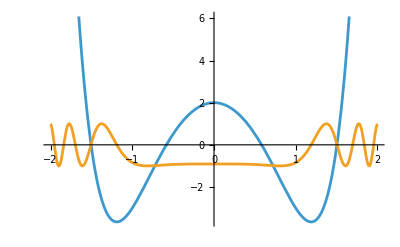

```mathematica
Plot[{g[x],h[x]},{x,-2,2}]
```

b) Nariši spodnjo sliko: zapolnjeni elipsi oranžne in zelene barve (prva  s središčem v (0,0), druga s središčem v (6,0), obe s polosema a=3,b=4) ter  rdeč krog s središčem v (3,0) in polmerom r=2.

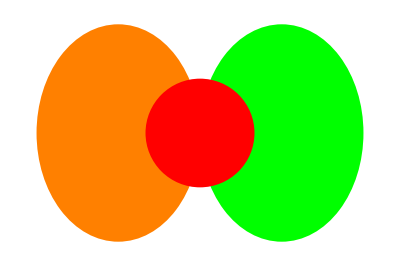

```mathematica
Graphics[{
Orange,Ellipsoid[{0,0},{3,4}],
Green,Ellipsoid[{6,0},{3,4}],
Red, Disk[{3,0},2]}]
```

c) Ponovno nariši zgornjo sliko, tokrat interaktivno tako, da se bo dalo rdečemu krogu spreminjati drugo koordinato središča na intervalu [-5,5]. Na sliki tudi označi vsa tri središča s črno točko.

```mathematica
Manipulate[Graphics[{
Orange,Ellipsoid[{0,0},{3,4}],
Green,Ellipsoid[{6,0},{3,4}],
Red, Disk[{3,a},2],
Black, Point[{0,0}],
Black, Point[{6,0}],
Black, Point[{3,a}]
}],{{a,0},-5,5}]
```

d) Napiši funkcijo `barve`, ki sprejme tri barve (barva1, barva2, barva3) in nariše sliko iz naloge b) tako, da je prva elipsa barve barva1, druga elipsa barve barva2 in krog barve barva3. (klic barve[Green,Purple,Yellow] naj vrne spodnjo sliko).

```mathematica
barve[barva1_,barva2_,barva3_]:= Graphics[{
barva1,Ellipsoid[{0,0},{3,4}],
barva2,Ellipsoid[{6,0},{3,4}],
barva3, Disk[{3,0},2]
}]
```

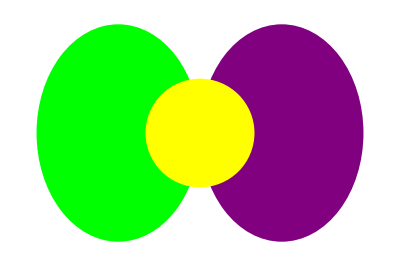

```mathematica
barve[Green,Purple,Yellow]
```